```mathematica
(* L1-norm calculation for MEMS-state under correlated ADC with memory: *)
```

```mathematica
(* Defining uncorrelated-ADC Kraus Operators for single qubit: *)
ClearAll[g,γ, μ,  p];
A0={{1, 0},{0,√(1-p)}};
A1={{0,√p}, {0, 0}};
A0//MatrixForm;
A1//MatrixForm;

(* Uncorrelated-ADC Kraus operators for two-qubits: *)
A00=KroneckerProduct[A0,A0];
A01=KroneckerProduct[A0,A1];
A10=KroneckerProduct[A1,A0];
A11=KroneckerProduct[A1,A1];

(* Correlated-ADC Kraus operators for two qubits: *)
B00 = {{√(1-p), 0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
B11= {{0,0,0,0},{0,0,0,0},{0,0,0,0},{√p,0,0,0}};
B00//MatrixForm;
B11//MatrixForm;

(* Checking the completeness of the Kraus operators: *)
A={{A00,A01,A10,A11}};
B={{B00,B11}};
FullSimplify[Sum[Transpose[A[[1,i]]].A[[1,i]],{i,1,4}]]//MatrixForm;
FullSimplify[Sum[Transpose[B[[1,i]]].B[[1,i]],{i,1,2}]]//MatrixForm;
```

```mathematica
(* MEMS-state density Matrix *)
ClearAll[g,γ,p,μ];
 ρ={{g,0,0,γ/2},{0,1-2g,0,0},{0,0,0,0},{γ/2,0,0,g}};
ρ//MatrixForm
Tr[ρ];

(* Density Matrix after evolution in correlated-ADC: *)
ρ1=(1-μ)*Sum[A[[1,i]].ρ.Transpose[A[[1,i]]],{i,1,4}]+μ*Sum[B[[1,i]].ρ.Transpose[B[[1,i]]],{i,1,2}]; 
Simplify[Tr[ρ1]]
ρ1//MatrixForm
```

(g | 0 | 0 | γ/2
0 | 1-2 g | 0 | 0
0 | 0 | 0 | 0
γ/2 | 0 | 0 | g)

1

((g+(1-2 g) p+g p^2) (1-μ)+g (1-p) μ | 0 | 0 | 1/2 (1-p) γ (1-μ)+1/2 √(1-p) γ μ
0 | ((1-2 g) (1-p)+g (1-p) p) (1-μ)+(1-2 g) μ | 0 | 0
0 | 0 | g (1-p) p (1-μ) | 0
1/2 (1-p) γ (1-μ)+1/2 √(1-p) γ μ | 0 | 0 | g (1-p)^2 (1-μ)+(g+g p) μ)

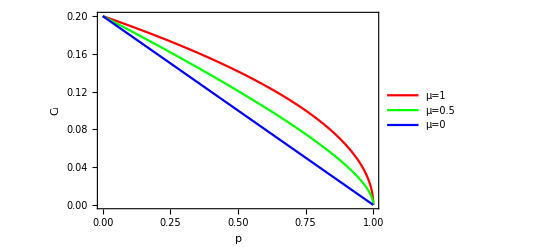

```mathematica
(*L1 norm of coherence: *)
ClearAll[g,γ, μ,  p];
γ=0.2;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ1[[i,j]]],0],{i,1,4},{j,1,4}];
Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_l"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

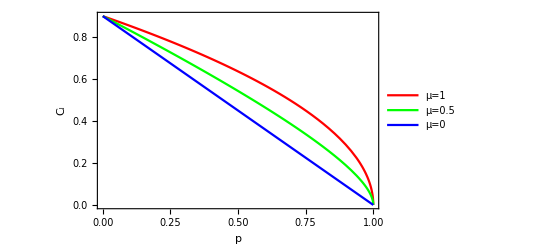

```mathematica
(*L1 norm of coherence: *)
ClearAll[g,γ, μ,  p];
γ=0.9;
g=γ/2;
L1=Sum[If[i!=j,Abs[ρ1[[i,j]]],0],{i,1,4},{j,1,4}];
Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_l"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

```mathematica
Relative Entropy of Coherence for a two-qubit density Matrix 
CR[ρ_]:=Module[{},
dg=Diagonal[ρ];
VNdg=Sum[-dg[[i]]*Log[2,dg[[i]]],{i,1,Length[dg]}];
eg=Eigenvalues[ρ];
 VNeg=Sum[If[eg[[i]]≠0,-eg[[i]]*Log[2,eg[[i]]],0],{i,1,Length[eg]}];
Cr=N[VNdg-VNeg]; 
Cr];

ClearAll[g,γ, μ,  p];
γ=1/5;
g=1/3;

 Plot[Evaluate@Table[CR[ρ1],{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_l"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

-density Matrix qubit+a Coherence Entropy for of Relative two

Infinity::indet: Indeterminate expression 0\ (-∞) encountered.

-Graphics-

```mathematica
Concurrence: Module 
 Conc[ρ_]:=Module[{srρ,RR,rhoflipped,lambdas,Concurrence,EV,Eigenwerte, ρflipped},
ρflipped=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]].Conjugate[ρ].KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
srρ=MatrixPower[ρ,1/2];
RR=MatrixPower[srρ.ρflipped.srρ,1/2];
EV=Chop[Eigenvalues[RR]];
Concurrence=If[Max[Abs[Im[EV]]]>0.0001,-1,
Eigenwerte=Sort[Re[EV],Greater];
N[Max[0,Eigenwerte[[1]]-Sum[Eigenwerte[[i]],{i,2,4}]]]];
Concurrence 
];

 ClearAll[g,γ, μ,  p];
γ=1/5;
g=1/3;
μ=1;
Plot[Evaluate@Table[Conc[ρ1],{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","Concurrence"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

Concurrence:Module

```mathematica
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
```

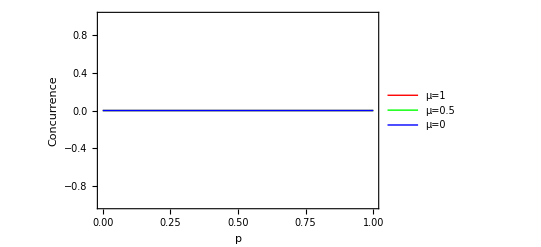

```mathematica
ClearAll[g,γ, μ,  p];
γ=1/5;
g=1/3;

Plot[Evaluate@Table[concurr[ρ1],{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","Concurrence"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

```mathematica
Concurrence: Plot
```

```mathematica
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
γ=1/5;
g=1/3;
μ=0;
```

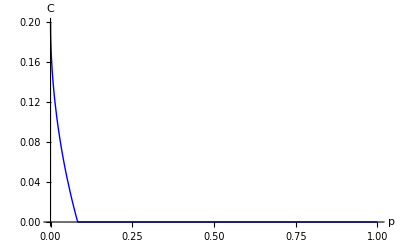

```mathematica
p1=Plot[N[concurr[ρ1]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8},PlotStyle->Blue]
```

```mathematica
μ=0.5;
```

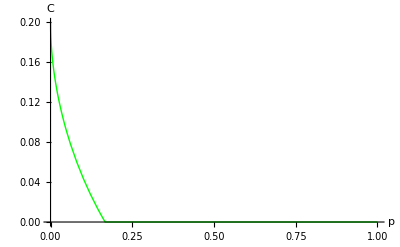

```mathematica
p2=Plot[N[concurr[ρ1]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8},PlotStyle->Green]
```

```mathematica
μ=1;
```

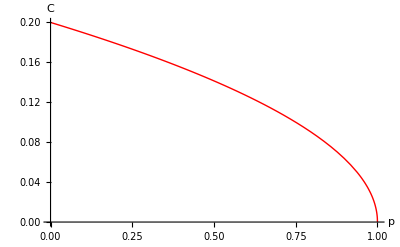

```mathematica
p3=Plot[N[concurr[ρ1]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Red]
```

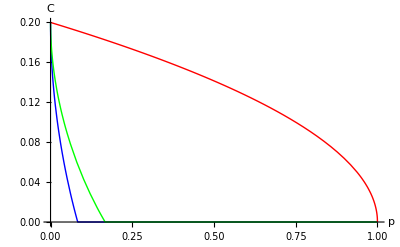

```mathematica
p4=Show[p1,p2,p3,PlotRange->All,FrameLabel->{"p","Concurrence"}, FrameStyle->Directive[Black,12]]
```